```mathematica
(*Introduction part a*)
{FullForm[a*b+c], FullForm[a+b*c]} (*showing what operations have precedence*)
```

{Plus[Times[a,b],c],Plus[a,Times[b,c]]}

```mathematica
a*b+c//f
```

f[a b+c]

```mathematica
f@a*b+c
```

c+b f[a]

```mathematica
FullForm[a*(b+c)] (*Using parentheses to specify order of operations*)
```

Times[a,Plus[b,c]]

```mathematica
∀_x∃_y x⊗y≻y ∧ m ≠ 0 ⇒ n ⧐̸ m
```

∀_x∃_y x⊗y≻y&&m≠0⇒n⧐̸m

```mathematica
FullForm[%] (*FullForm shows the structure of the expression*)
```

Implies[And[ForAll[x,Exists[y,Succeeds[CircleTimes[x,y],y]]],Unequal[m,0]],NotRightTriangleBar[n,m]]

```mathematica
{x->#^2&,(x->#^2)&,x->(#^2&)}
```

{x→#1^2&,x→#1^2&,x→(#1^2&)}

```mathematica
(*There are flat, left grouping, and right grouping types of operators*)
(*Plus is a flat operator, no grouping is necessary*)
FullForm[a+b+c+d]
```

Plus[a,b,c,d]

```mathematica
FullForm[a^b^c^d] (*not flat so it gets grouped in pairs*)
```

Power[a,Power[b,Power[c,d]]]

```mathematica
(*some special characters are operators as well*)
a⊕b⊕c//FullForm
```

CirclePlus[a,b,c]

```mathematica
a×a×a×b×b×c (*× means same as '*'*)
```

a^3 b^2 c

```mathematica
∫k[x] ⅆx//FullForm
```

Integrate[k[x],x]

```mathematica
∫a[x] b[x] ⅆx+c[x]
```

c[x]+∫a[x] b[x]ⅆx

```mathematica
x^(a+b)
```

x^(a+b)

```mathematica
\!\(\*SubscriptBox[\(∂\),\(x\)]\*SuperscriptBox[\(x\),\(n\)]\)
```

n x^(-1+n)

```mathematica
∂_x x^n (*What I typed above is supposed to look like this*)
```

n x^(-1+n)

```mathematica
∑_(n=1)^∞ 1/n^s
```

Zeta[s]

```mathematica
∑_(n=1)^∞ 1/n^s + n
```

n+Zeta[s]

```mathematica
(*Introduction part b*)
Factor[x^6-1]
```

(-1+x) (1+x) (1-x+x^2) (1+x+x^2)

```mathematica
FullForm[{a,b,c}] (*can label diff types of data to be used by later operands such as creating a list*)
```

List[a,b,c]

```mathematica
point[a,b,c] (*point does nothing but store these under the head point so they can be used later*)
```

point[a,b,c]

```mathematica
(*Introduction part c*)
(*4 differnt types of brackets:
parentheses for grouping, square brackets for functions, curly braces for lists, and double brackets for indexing*)
```

```mathematica
(*Introduction part d*)
1+2/3
```

5/3

```mathematica
(1+2)/3 (*effect of parentheses for grouping*)
```

1

```mathematica
{1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
{1,b,2,3,3x==12,Sqrt[9+y],"hello"} (*lists can contain anything*)
```

{1,b,2,3,3 x==12,√(9+y),hello}

```mathematica
{1,1,{3,4,5},{3,2}} (*lists can contain other lists*)
```

{1,1,{3,4,5},{3,2}}

```mathematica
(*Square brackets enclose the arguments of functions*)
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Sin[2]
```

Sin[2]

```mathematica
N[Sin[2]]
```

0.909297

```mathematica
v=Range[10]^2
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
v[[3]] (*double square brackets used for indexing*)
```

9

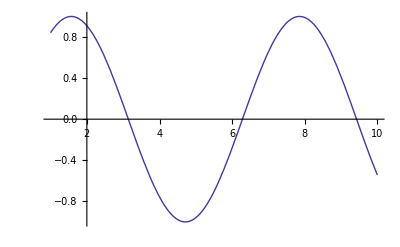

```mathematica
(*Plot a function,with the range of the plot specified in a list*)
Plot[Sin[x],{x,1,10}]
```

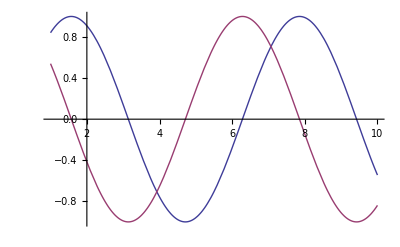

```mathematica
(*Plot two functions togetherthe pair of functions is in a list*)
Plot[{Sin[x],Cos[x]},{x,1,10}]
```

```mathematica
(*Symbolic Analysis part a*)
3+62-1 (*numerical computation*)
```

64

```mathematica
3x-x+2 (*symbolic*)
```

2+2 x

```mathematica
-1+2 x+x^3
```

-1+2 x+x^3

```mathematica
x^2+x-4 x^2 (*simplifying algebraic expressions*)
```

x-3 x^2

```mathematica
x y+2 x^2 y+y^2 x^2-2 y x
```

-x y+2 x^2 y+x^2 y^2

```mathematica
(x+2 y+1) (x-2)^2
```

(-2+x)^2 (1+x+2 y)

```mathematica
(*The function Expand multiplies out products and powers*)
Expand[%]
```

4-3 x^2+x^3+8 y-8 x y+2 x^2 y

```mathematica
(*Factor does essentially the inverse of Expand*)
Factor[%]
```

(-2+x)^2 (1+x+2 y)

```mathematica
Sqrt[2]/9801 (4 n)! (1103+26390 n)/(n!^4 396^(4 n)) (*make sure parentheses are in the right places*)
```

(2^(1/2-8 n) 99^(-2-4 n) (1103+26390 n) (4 n)!)/(n!)^4

```mathematica
(*Mathematica uses standard rules of algebra to replace sqrt(1+x)^4 by (1+x)^2*)
Sqrt[1+x]^4
```

(1+x)^2

```mathematica
(*Mathematica knows no rules for this expression,so it leaves the expression in the original form you gave*)
Log[1+Cos[x]]
```

Log[1+Cos[x]]

```mathematica
(*Symbolic Analysis part b*)
1+2 x /. x-> 3
```

7

```mathematica
1+x+x^2 /. x -> 2-y
```

3+(2-y)^2-y

```mathematica
x -> 3+y
```

x→3+y

```mathematica
(*This applies the transformation rule on the previous line*)
x^2-9 /. %
```

-9+(3+y)^2

```mathematica
(*You can apply rules together by putting the rules in a list*)
(x+y) (x-y)^2 /. {x -> 3, y -> 1-a}
```

(4-a) (2+a)^2

```mathematica
(*assigning values to variables*)
x=3
```

3

```mathematica
x^2-1
```

8

```mathematica
x=1+a
```

1+a

```mathematica
x^2-1
```

-1+(1+a)^2

```mathematica
(*This removes the value you assigned to*)
x=.
```

```mathematica
x+5-2 x
```

5-x

```mathematica
t=1+x^2
```

1+x^2

```mathematica
t/.x->2
```

5

```mathematica
t/.x->5 a
```

1+25 a^2

```mathematica
t/.x->Pi//N (*finds the value of when is replaced by Pi,and then evaluates the result numerically*)
```

10.8696

```mathematica
(*Symbolic Analysis part c*)
(*Expand gives the "expanded form",with products and powers multiplied ou*)
Expand[(1+x)^2]
```

1+2 x+x^2

```mathematica
(*Factor recovers the original form*)
Factor[%]
```

(1+x)^2

```mathematica
Expand[(1+x+3 y)^4]
```

1+4 x+6 x^2+4 x^3+x^4+12 y+36 x y+36 x^2 y+12 x^3 y+54 y^2+108 x y^2+54 x^2 y^2+108 y^3+108 x y^3+81 y^4

```mathematica
Factor[%]
```

(1+x+3 y)^4

```mathematica
Factor[x^10-1]
```

(-1+x) (1+x) (1-x+x^2-x^3+x^4) (1+x+x^2+x^3+x^4)

```mathematica
Expand[%]
```

-1+x^10

```mathematica
(*Symbolic Analysis part d*)
(*Simplify writes in factored form*)
Simplify[x^2+2 x+1]
```

(1+x)^2

```mathematica
(*Simplify leaves in expanded form,since for this expression,the factored form is large*)
Simplify[x^10-1]
```

-1+x^10

```mathematica
Integrate[1/(x^4-1),x]
```

-ArcTan[x]/2+1/4 Log[1-x]-1/4 Log[1+x]

```mathematica
D[%,x] (*Differentiating it back gives more complicated expression than original*)
```

-1/(4 (1-x))-1/(4 (1+x))-1/(2 (1+x^2))

```mathematica
Simplify[%]
```

1/(-1+x^4)

```mathematica
Simplify[Gamma[x] Gamma[1-x]] (*Simplify does nothing*)
```

Gamma[1-x] Gamma[x]

```mathematica
FullSimplify[Gamma[x] Gamma[1-x]] (*FullSimplify works though*)
```

π Csc[π x]

```mathematica
(*Calculus part a*)
D[x^n,x] (*first derivative wrt x*)
```

n x^(-1+n)

```mathematica
(*3rd derivative*)
D[x^n,{x,3}]
```

(-2+n) (-1+n) n x^(-3+n)

```mathematica
D[x[1]^2+x[2]^2,x[1]]
```

2 x[1]

```mathematica
(*D does partial differentiation.It assumes here that y is independent of x*)
D[x^2+y^2,x]
```

2 x

```mathematica
(*If does in fact depend on x,you can use the explicit functional form y[x]*)
D[x^2+y[x]^2,x]
```

2 x+2 y[x] y'[x]

```mathematica
D[x^2+y^2,x,NonConstants->{y}]
```

2 x+2 y D[y,x,NonConstants→{y}]

```mathematica
(*This gives the gradient of the func x^2+y^2*)
D[x^2+y^2,{{x,y}}]
```

{2 x,2 y}

```mathematica
(*This gives the Hessian*)
D[x^2+y^2,{{x,y},2}]
```

{{2,0},{0,2}}

```mathematica
(*The Jacobian*)
D[{x^2+y^2,x y},{{x,y}}]
```

{{2 x,2 y},{y,x}}

```mathematica
(*Calculus part b - Integration*)
Integrate[x^n,x]
```

x^(1+n)/(1+n)

```mathematica
Integrate[1/(x^4-a^4),x] (*Sometimes the integrals are really complicated and give weird answers*)
```

-ArcTan[x/a]/(2 a^3)+Log[a-x]/(4 a^3)-Log[a+x]/(4 a^3)

```mathematica
Integrate[Log[1-x^2],x]
```

-2 x-Log[1-x]+Log[1+x]+x Log[1-x^2]

```mathematica
Integrate[Log[1-x^2]/x,x]
```

-1/2 PolyLog[2,x^2]

```mathematica
Integrate[Exp[1-x^2],x]
```

1/2 ⅇ √π Erf[x]

```mathematica
Integrate[Sin[x^2],x]
```

√(π/2) FresnelS[√(2/π) x]

```mathematica
Integrate[(1-x^2)^n,x]
```

x Hypergeometric2F1[1/2,-n,3/2,x^2]

```mathematica
Integrate[x^x,x] (*Sometimes they can't be done at all*)
```

∫x^x ⅆx

```mathematica
(*Definite integrals*)
Integrate[Sin[x]^2,{x,a,b}]
```

1/2 (-a+b+Cos[a] Sin[a]-Cos[b] Sin[b])

```mathematica
Integrate[Exp[-x^2],{x,0,Infinity}]
```

(√π)/2

```mathematica
Integrate[x^x,{x,0,1}]
```

∫_0^1 x^x ⅆx

```mathematica
N[%] (*can't get a formula, but can get a numerical result*)
```

0.783431

```mathematica
(*double integral*)
Integrate[x^2+y^2,{x,0,1},{y,0,x}]
```

1/3

```mathematica
(*integrates x^10 over circular region*)
Integrate[x^10Boole[x^2+y^2≤1],{x,-1,1},{y,-1,1}]
```

(21 π)/512

```mathematica
(*Calculus part c - Indefinite Integrals*)
Integrate[x^2,x]
```

x^3/3

```mathematica
D[%+c,x]
```

x^2

```mathematica
Integrate[1/(x^2-1),x]
```

1/2 Log[1-x]-1/2 Log[1+x]

```mathematica
D[%,x] (*Should give back orig func*)
```

-1/(2 (1-x))-1/(2 (1+x))

```mathematica
Simplify[%] (*it does*)
```

1/(-1+x^2)

```mathematica
Integrate[a x^2,x] (*assumes a is a constant*)
```

(a x^3)/3

```mathematica
Integrate[x b[x]^2,b[x]]
```

1/3 x b[x]^3

```mathematica
(*Mathematica gives the standard result for this integral,implicitly assuming that n is not equal to -1*)
Integrate[x^n,x]
```

x^(1+n)/(1+n)

```mathematica
(*If you specifically give an exponent of -1,Mathematica produces a different result*)
Integrate[x^-1,x]
```

Log[x]

```mathematica
Integrate[1/(1+a x^2),x]
```

ArcTan[√a x]/(√a)

```mathematica
(*Integrate chooses the simplest form of the answer*)
Simplify[D[{ArcTan[x],-ArcTan[1/x]},x]]
```

{1/(1+x^2),1/(1+x^2)}

```mathematica
Integrate[1/(1+x^2),x]
```

ArcTan[x]

```mathematica
(*Calculus part d - Differential Equations*)
DSolve[y'[x]+y[x]==1,y[x],x]
```

{{y[x]→1+ⅇ^-x C[1]}}

```mathematica
{{y[x]->1+ⅇ^-x C[1]}}
```

{{y[x]→1+ⅇ^-x C[1]}}

```mathematica
y[x]+2 y'[x]+y[0]/.% (*so the answer does not work for y'[x] or y[0]*)
```

{1+ⅇ^-x C[1]+y[0]+2 y'[x]}

```mathematica
DSolve[y'[x]+y[x]==1,y,x]
```

{{y→Function[{x},1+ⅇ^-x C[1]]}}

```mathematica
DSolve[y'[x]+y[x]==1,y[x],x];
y[x]+2 y'[x]+y[0]/.%;
y'[x]+y[x]==1/.%%
```

{1+ⅇ^-x C[1]+y'[x]==1}

```mathematica
(*Solving simultaneous diff equations*)
DSolve[{y[x]==-z'[x],z[x]==-y'[x]},{y,z},x]
```

{{y→Function[{x},1/2 ⅇ^-x (1+ⅇ^(2 x)) C[1]-1/2 ⅇ^-x (-1+ⅇ^(2 x)) C[2]],z→Function[{x},-1/2 ⅇ^-x (-1+ⅇ^(2 x)) C[1]+1/2 ⅇ^-x (1+ⅇ^(2 x)) C[2]]}}

```mathematica
DSolve[y[x] y'[x]==1,y,x]
```

{{y→Function[{x},-√2 √(x+C[1])]},{y→Function[{x},√2 √(x+C[1])]}}

```mathematica
(*adding boundary conditions*)
DSolve[{y'[x]==a y[x],y[0]==1},y[x],x]
```

{{y[x]→ⅇ^(a x)}}

```mathematica
(*if no boundary conditions, will add undetermined constants*)
DSolve[y''''[x]==y[x], y[x],x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^-x C[3]+C[2] Cos[x]+C[4] Sin[x]}}

```mathematica
DSolve[{y''''[x]==y[x],y[0]==y'[0]==0},y[x],x] (*adding boundary cond reduces these constants*)
```

{{y[x]→ⅇ^-x (-C[1]+ⅇ^(2 x) C[1]-C[2]+ⅇ^x C[2] Cos[x]-2 ⅇ^x C[1] Sin[x]-ⅇ^x C[2] Sin[x])}}

```mathematica
(*Some equations can only be solved using special functions*)
DSolve[y''[x]-x y[x]==0,y[x],x]
```

{{y[x]→AiryAi[x] C[1]+AiryBi[x] C[2]}}

```mathematica
DSolve[y''[x]-Exp[x] y[x]==0,y[x],x]
```

{{y[x]→BesselI[0,2 √(ⅇ^x)] C[1]+2 BesselK[0,2 √(ⅇ^x)] C[2]}}

```mathematica
DSolve[y''[x]+Cos[x] y[x]==0,y,x]
```

{{y→Function[{x},C[1] MathieuC[0,-2,x/2]+C[2] MathieuS[0,-2,x/2]]}}

```mathematica
DSolve[y''[x]-Cot[x]^2 y[x]==0,y[x],x]
```

{{y[x]→C[1] (-1+Cos[x]^2)^(1/4) LegendreP[1/2,(√5)/2,Cos[x]]+C[2] (-1+Cos[x]^2)^(1/4) LegendreQ[1/2,(√5)/2,Cos[x]]}}

```mathematica
DSolve[x^2 y''[x]+y[x]==0,y[x],x] (*ex of 2nd order diff equation that can be solved with elementary function*)
```

{{y[x]→√x C[1] Cos[1/2 √3 Log[x]]+√x C[2] Sin[1/2 √3 Log[x]]}}

```mathematica
DSolve[y'[x]-y[x]^2==0,y[x],x]
```

{{y[x]→1/(-x-C[1])}}

```mathematica
DSolve[y'[x]+x y[x]^3+y[x]^2==0,y[x],x] (*can be solved only implicitly*)
```

```mathematica
Solve[1/2 ((2 ArcTanh[(-1-2 x y[x])/(√5)])/(√5)+Log[(-1-x y[x] (-1-x y[x]))/(x^2 y[x]^2)])==C[1]-Log[x],y[x]]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[1/2 ((2 ArcTanh[(-1-2 x y[x])/(√5)])/(√5)+Log[(-1-x y[x] (-1-x y[x]))/(x^2 y[x]^2)])==C[1]-Log[x],y[x]]

```mathematica
(*Partial Differential equations*)
DSolve[D[y[x1,x2],x1]+D[y[x1,x2],x2]==1/(x1 x2),y[x1,x2],{x1,x2}]
```

{{y[x1,x2]→(-Log[x1]+Log[x2]+x1 C[1][-x1+x2]-x2 C[1][-x1+x2])/(x1-x2)}}

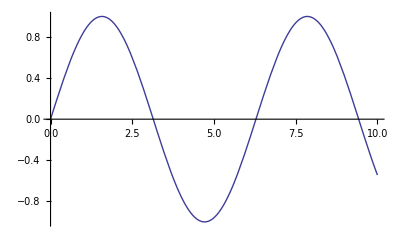

```mathematica
(*Plotting part a*)
Plot[Sin[x],{x,0,10}]
```

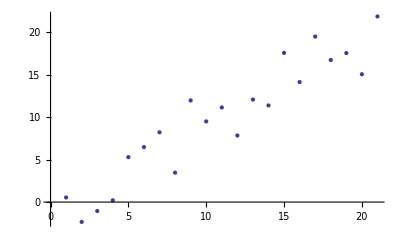

```mathematica
datapts=Table[x+RandomReal[{-4,4}],{x,0,20}];
ListPlot[datapts]
```

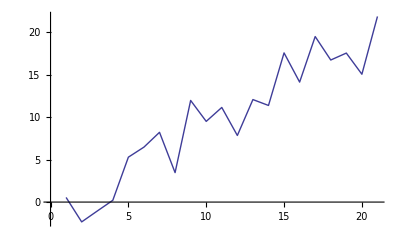

```mathematica
ListLinePlot[datapts]
```

```mathematica
(*Plot3D[Sin[x] Cos[y],{x,0,5},{y,1,10}]*)
```

```mathematica
(*GraphicsGrid[{{Plot3D[Sin[x] Cos[y],{x,0,5},{y,1,10}],Plot3D[Sin[x]*Cos[y],{x,0,5},{y,1,10},ColorFunction->(Hue[#3]&),MeshFunctions->(#3&),Boxed->False,Axes->False]}}]*)
```

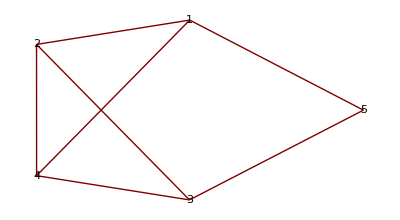

```mathematica
GraphPlot[{1->2,1->4,2->4,3->4,3->2,3->5,5->1},VertexLabeling->True]
```

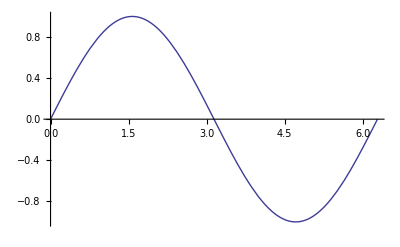

```mathematica
(*Plotting Part b*)
Plot[Sin[x],{x,0,2 Pi}]
```

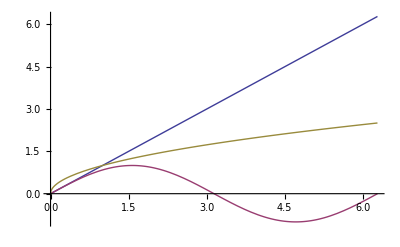

```mathematica
Plot[{x,Sin[x],Sqrt[x]},{x,0,2 Pi}]
```

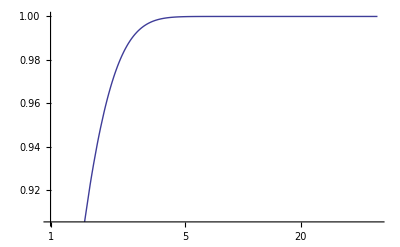

```mathematica
LogLinearPlot[Tanh[x],{x,1,50}]
```

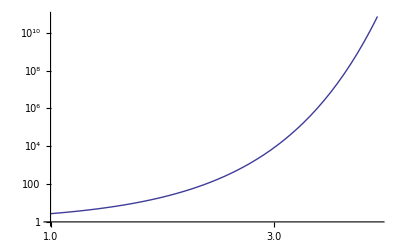

```mathematica
LogLogPlot[E^x^2,{x,1,5}]
```

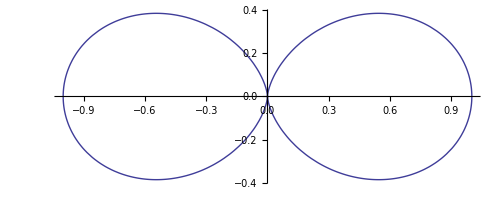

```mathematica
t=.
PolarPlot[Cos[t]^2,{t,0,2 Pi}]
```

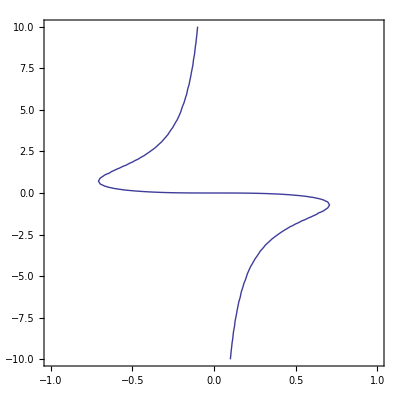

```mathematica
ContourPlot[x^3+x y^2+y==0,{x,-1,1},{y,-10,10}]
```